## Scientific Programming 1

Using Mathematica as a calculator

```mathematica
1000!
```

402387260077093773543702433923003985719374864210714632543799910429938512398629020592044208486969404800479988610197196058631666872994808558901323829669944590997424504087073759918823627727188732519779505950995276120874975462497043601418278094646496291056393887437886487337119181045825783647849977012476632889835955735432513185323958463075557409114262417474349347553428646576611667797396668820291207379143853719588249808126867838374559731746136085379534524221586593201928090878297308431392844403281231558611036976801357304216168747609675871348312025478589320767169132448426236131412508780208000261683151027341827977704784635868170164365024153691398281264810213092761244896359928705114964975419909342221566832572080821333186116811553615836546984046708975602900950537616475847728421889679646244945160765353408198901385442487984959953319101723355556602139450399736280750137837615307127761926849034352625200015888535147331611702103968175921510907788019393178114194545257223865541461062892187960223838971476088506276862967146674697562911234082439208160153780889893964518263243671616762179168909779911903754031274622289988005195444414282012187361745992642956581746628302955570299024324153181617210465832036786906117260158783520751516284225540265170483304226143974286933061690897968482590125458327168226458066526769958652682272807075781391858178889652208164348344825993266043367660176999612831860788386150279465955131156552036093988180612138558600301435694527224206344631797460594682573103790084024432438465657245014402821885252470935190620929023136493273497565513958720559654228749774011413346962715422845862377387538230483865688976461927383814900140767310446640259899490222221765904339901886018566526485061799702356193897017860040811889729918311021171229845901641921068884387121855646124960798722908519296819372388642614839657382291123125024186649353143970137428531926649875337218940694281434118520158014123344828015051399694290153483077644569099073152433278288269864602789864321139083506217095002597389863554277196742822248757586765752344220207573630569498825087968928162753848863396909959826280956121450994871701244516461260379029309120889086942028510640182154399457156805941872748998094254742173582401063677404595741785160829230135358081840096996372524230560855903700624271243416909004153690105933983835777939410970027753472000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000

```mathematica
N[π,1000]
```

3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117067982148086513282306647093844609550582231725359408128481117450284102701938521105559644622948954930381964428810975665933446128475648233786783165271201909145648566923460348610454326648213393607260249141273724587006606315588174881520920962829254091715364367892590360011330530548820466521384146951941511609433057270365759591953092186117381932611793105118548074462379962749567351885752724891227938183011949129833673362440656643086021394946395224737190702179860943702770539217176293176752384674818467669405132000568127145263560827785771342757789609173637178721468440901224953430146549585371050792279689258923542019956112129021960864034418159813629774771309960518707211349999998372978049951059731732816096318595024459455346908302642522308253344685035261931188171010003137838752886587533208381420617177669147303598253490428755468731159562863882353787593751957781857780532171226806613001927876611195909216420199

```mathematica
N[Sin[2017 2^(1/5)],40]
```

-0.9999999999999999785677712610609832590685

```mathematica
N[(4034 2^(1/5))/(1475π),40]
```

1.000000000002825769728299060506259313476

```mathematica
TrigReduce[Sin[θ]^27]
```

1/67108864(20058300 Sin[θ]-17383860 Sin[3 θ]+13037895 Sin[5 θ]-8436285 Sin[7 θ]+4686825 Sin[9 θ]-2220075 Sin[11 θ]+888030 Sin[13 θ]-296010 Sin[15 θ]+80730 Sin[17 θ]-17550 Sin[19 θ]+2925 Sin[21 θ]-351 Sin[23 θ]+27 Sin[25 θ]-Sin[27 θ])

```mathematica
2^100+1
```

1267650600228229401496703205377

```mathematica
FactorInteger[%]
```

{{17,1},{401,1},{61681,1},{340801,1},{2787601,1},{3173389601,1}}

```mathematica
int=∫1/(1-x^5)ⅆx
```

1/20 (2 √(2 (5+√5)) ArcTan[(1-√5+4 x)/(√(2 (5+√5)))]+2 √(10-2 √5) ArcTan[(1+√5+4 x)/(√(10-2 √5))]-4 Log[1-x]-(-1+√5) Log[1-1/2 (-1+√5) x+x^2]+(1+√5) Log[1+1/2 (1+√5) x+x^2])

```mathematica
int//TraditionalForm
```

1/20 (-(√5-1) log(x^2-1/2 (√5-1) x+1)+(1+√5) log(x^2+1/2 (1+√5) x+1)-4 log(1-x)+2 √(2 (5+√5)) tan^-1((4 x-√5+1)/(√(2 (5+√5))))+2 √(10-2 √5) tan^-1((4 x+√5+1)/(√(10-2 √5))))

```mathematica
%//TeXForm
```

\frac{1}{20} \left(-\left(\sqrt{5}-1\right) \log \left(x^2-\frac{1}{2} \left(\sqrt{5}-1\right)
   x+1\right)+\left(1+\sqrt{5}\right) \log \left(x^2+\frac{1}{2} \left(1+\sqrt{5}\right)
   x+1\right)-4 \log (1-x)+2 \sqrt{2 \left(5+\sqrt{5}\right)} \tan ^{-1}\left(\frac{4
   x-\sqrt{5}+1}{\sqrt{2 \left(5+\sqrt{5}\right)}}\right)+2 \sqrt{10-2 \sqrt{5}} \tan
   ^{-1}\left(\frac{4 x+\sqrt{5}+1}{\sqrt{10-2 \sqrt{5}}}\right)\right)

```mathematica
D[int, x]
```

1/20 (4/(1-x)-((-1+√5) (1/2 (1-√5)+2 x))/(1-1/2 (-1+√5) x+x^2)+((1+√5) (1/2 (1+√5)+2 x))/(1+1/2 (1+√5) x+x^2)+8/(1+(1-√5+4 x)^2/(2 (5+√5)))+8/(1+(1+√5+4 x)^2/(10-2 √5)))

```mathematica
Simplify[%]
```

1/(1-x^5)

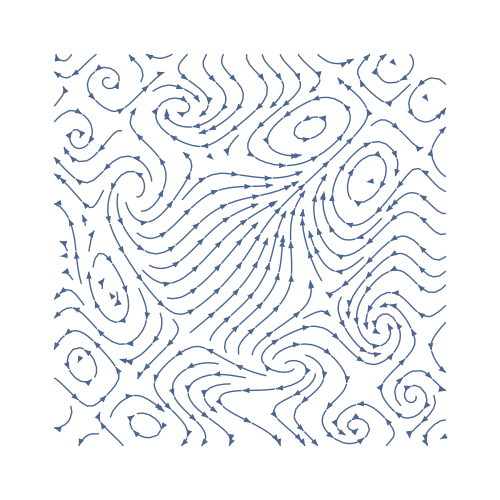

```mathematica
strm=
StreamPlot[{Cos[-1-x+y^2], Sin[1+x^2-y]},{x,-3,3},{y,-3,3}, 
                      Frame->None ,ImageSize->500]
```

```mathematica
Plot3D[Sin[-1-x+y^2],{x,-3,3},{y,-3,3},
              PlotPoints->100,
              PlotStyle->Texture[strm],
              Mesh->None,
              BoxRatios->{1, 1, 0.5},
              ImageSize->600
                ]
```

-Graphics3D-

```mathematica
positions=ProteinData["KLKB1","AtomPositions","Residue"];
```

```mathematica
Length[positions⟦All,2⟧]
```

238

```mathematica
Take[positions⟦All,2⟧,10]//Column
```

{3817.8,3403.5,490.7}
{3480.6,3281.,358.}
{3287.7,3517.6,123.4}
{3571.8,3772.1,100.7}
{3751.7,3938.1,-192.8}
{4115.8,4022.2,-280.2}
{4289.5,4297.6,-82.8}
{4524.5,4558.8,-237.6}
{4879.9,4667.8,-152.6}
{4889.1,4886.9,161.8}

```mathematica
Graphics3D[
Tube[
BezierCurve[positions⟦All,2⟧], 80],
ImageSize->Large
                       ]
```

-Graphics3D-

```mathematica
earth=AstronomicalData["Earth","Image"]
```

-Graphics-

Everything is an expression

```mathematica
{a,b,c}//FullForm
```

List[a,b,c]

```mathematica
a+b//FullForm
```

Plus[a,b]

```mathematica
a b//FullForm
```

Times[a,b]

```mathematica
1/2//FullForm (* *)
```

Rational[1,2]

```mathematica
FullForm/@{(2π)/5,(2π)/5.0}  (*/@ for both*)
(*5 vs 5.0*)
```

{Times[Rational[2,5],Pi],1.25664}

```mathematica
Sin/@{(2π)/5,(2π)/5.0}
```

{√(5/8+(√5)/8),0.951057}

```mathematica
a x^2+ b x + c//FullForm
```

Plus[c,Times[b,x],Times[a,Power[x,2]]]

```mathematica
Series[Exp[Sin[x]],{x,0,10}]
```

1+x+x^2/2-x^4/8-x^5/15-x^6/240+x^7/90+(31 x^8)/5760+x^9/5670-(2951 x^10)/3628800+O[x]^11

```mathematica
FullForm[%]
```

SeriesData[x,0,List[1,1,Rational[1,2],0,Rational[-1,8],Rational[-1,15],Rational[-1,240],Rational[1,90],Rational[31,5760],Rational[1,5670],Rational[-2951,3628800]],0,11,1]

```mathematica
%⟦3⟧ (*the coefficients are in position 3 in the series data*)
```

{1,1,1/2,0,-1/8,-1/15,-1/240,1/90,31/5760,1/5670,-2951/3628800}

```mathematica
Head/@{a+b, a b,π,2,2.0,1/2,2+ⅈ,lena}  (*Expression is a list with a head*)
```

{Plus,Times,Symbol,Integer,Real,Rational,Complex,Symbol}

```mathematica
c=a+1/2
```

1/2+a

```mathematica
AtomQ[c](*Things that cannot be simplified are 'atoms'*)
(* c has parts, it isn't an atom*)
```

False

```mathematica
c//FullForm
```

Plus[Rational[1,2],a]

```mathematica
c⟦1⟧ (*while c[[2]] is a, from the above fullform*)
```

1/2

```mathematica
AtomQ[%] (*so 1/2 is an atom*)
```

True

```mathematica
c⟦1,1⟧
```

Part::partd: Part specification (1/2+a)⟦1,1⟧ is longer than depth of object.

(1/2+a)⟦1,1⟧

```mathematica
Clear[c]
```

```mathematica
AtomQ["this is an atom"](*a string is an atom*)
```

True

```mathematica
"this is an atom"⟦1⟧
```

Part::partd: Part specification this is an atom⟦1⟧ is longer than depth of object.

this is an atom⟦1⟧

```mathematica
"this is an atom"⟦0⟧ (*returns the head of this*)
```

String

```mathematica
N[π]
```

3.14159

```mathematica
AtomQ[%]
```

True

```mathematica
?AtomQ
```

AtomQ[expr] yields True if expr is an expression which cannot be divided into subexpressions, and yields False otherwise.

```mathematica
Clear[c]
```

```mathematica
Append[{a,b},c]
```

{a,b,c}

```mathematica
Append[f[a,b],c] (*because f[a,b] is a list with head f, so appending c adds another argument*)
```

f[a,b,c]

```mathematica
Head[%]
```

f

```mathematica
earth
```

-Graphics-

```mathematica
Blur[earth,5]
```

-Graphics-

```mathematica
earth//FullForm
```

Image[RawArray["UnsignedInteger8",List[List[List[3,1,2],List[3,1,2],List[3,1,2],List[3,1,2],List[3,1,2],List[3,1,2],List[3,1,2],List[3,1,2],List[3,1,2],List[3,1,2],List[3,1,2],List[3,1,2],List[3,1,2],List[3,1,4],List[3,1,4],List[3,1,4],List[3,1,4],List[3,1,4],List[3,1,4],List[3,1,4],List[3,1,4],List[3,1,4],List[3,1,4],List[3,1,4],List[3,1,4],List[5,0,4],List[5,0,4],List[5,1,2],List[5,1,2],List[5,1,2],List[5,1,2],List[5,1,0],List[7,1,3],List[7,3,2],52,List[5,0,6],List[5,0,6],List[5,0,6],List[3,1,4],List[2,2,2],List[2,2,2],List[2,2,2],List[2,2,2],List[2,2,2],List[2,2,2],List[2,2,2],List[2,2,2],List[2,2,2],List[2,2,2],List[2,2,2],List[2,2,2],List[2,2,2],List[2,2,2],List[2,2,2],List[2,2,2],List[2,2,2],List[2,2,2],List[2,2,2],List[2,2,2],List[2,2,2],List[2,2,2],List[2,2,2],List[2,2,2],List[2,2,2],List[2,2,2],List[2,2,2],List[2,2,2],List[2,2,2],List[2,2,2]],119]],"Byte",1,Rule[1]]
 |  |  |  |

$OutputSizeLimit::nosess: This output can only be updated in the same kernel session that generated it.

Assignments

```mathematica
r1=RandomReal[] (*Setting r1 to this value*)
```

0.148339

```mathematica
r2:=RandomReal[] (*This, however, is a RULE that sets a=b WHEN it's called*)
```

```mathematica
?SetDelayed
?Set
```

lhs:=rhs assigns rhs to be the delayed value of lhs. rhs is maintained in an unevaluated form. When lhs appears, it is replaced by rhs, evaluated afresh each time.

lhs=rhs evaluates rhs and assigns the result to be the value of lhs. From then on, lhs is replaced by rhs whenever it appears. 
{l_1,l_2,…}={r_1,r_2,…} evaluates the r_i, and assigns the results to be the values of the corresponding l_i.

```mathematica
Table[r1,{5}]
```

{0.148339,0.148339,0.148339,0.148339,0.148339}

```mathematica
Table[r2,{5}]
```

{0.463731,0.996927,0.515966,0.314558,0.70654}

```mathematica
r1
```

0.148339

```mathematica
r2
```

0.710888

```mathematica
Clear[a,b,c]
```

```mathematica
Clear[r1,r2]
```

```mathematica
(*************************************)
(*Fibonacci Numbers*)
fib[n_]:=0/;n≤0  (*Set conditions by using /; as shown*)
fib[1]=1;
fib[n_]:=fib[n-1]+fib[n-2]
```

```mathematica
fib[2]
```

1

```mathematica
fib[3]
```

2

```mathematica
fib[20]
```

6765

```mathematica
fib[30]//Timing (*Apparently thid does fib[30]=832040 evaluations*)
```

{2.4375,832040}

```mathematica
fib[31]//Timing
```

{4.03125,1346269}

```mathematica
Remove[fib] (*Remove the function*)
```

```mathematica
fib[n_]:=0/;n≤0
fib[1]=1;
fib[n_]:=fib[n]=fib[n-1]+fib[n-2] (*This makes it remember the intermmediate stages!!!, so it will remember them next time*)
```

```mathematica
fib[30]//Timing
```

{0.,832040}

```mathematica
fib[50]//Timing
```

{0.,12586269025}

```mathematica
?fib
```

Global`fib

fib[1]=1
 
fib[2]=1
 
fib[3]=2
 
fib[4]=3
 
fib[5]=5
 
fib[6]=8
 
fib[7]=13
 
fib[8]=21
 
fib[9]=34
 
fib[10]=55
 
fib[11]=89
 
fib[12]=144
 
fib[13]=233
 
fib[14]=377
 
fib[15]=610
 
fib[16]=987
 
fib[17]=1597
 
fib[18]=2584
 
fib[19]=4181
 
fib[20]=6765
 
fib[21]=10946
 
fib[22]=17711
 
fib[23]=28657
 
fib[24]=46368
 
fib[25]=75025
 
fib[26]=121393
 
fib[27]=196418
 
fib[28]=317811
 
fib[29]=514229
 
fib[30]=832040
 
fib[31]=1346269
 
fib[32]=2178309
 
fib[33]=3524578
 
fib[34]=5702887
 
fib[35]=9227465
 
fib[36]=14930352
 
fib[37]=24157817
 
fib[38]=39088169
 
fib[39]=63245986
 
fib[40]=102334155
 
fib[41]=165580141
 
fib[42]=267914296
 
fib[43]=433494437
 
fib[44]=701408733
 
fib[45]=1134903170
 
fib[46]=1836311903
 
fib[47]=2971215073
 
fib[48]=4807526976
 
fib[49]=7778742049
 
fib[50]=12586269025
 
fib[n_]:=0/;n≤0
 
fib[n_]:=fib[n]=fib[n-1]+fib[n-2]

```mathematica
m={{1,1},{1,0}}; (*Let us now try to make a better algorithm so (Subscript[F, n], Subscript[F, n-1])=m(Subscript[F, n-1], Subscript[F, n-2]) and start with (1,0)*)
```

```mathematica
f[n_]:=MatrixPower[m,n]⟦2,1⟧ (*extract the [2,1] component*)(*And now there are log n multipliccations!!!*)
```

```mathematica
f[50]
```

12586269025

```mathematica
f[10^6]
```

```mathematica
N[%]
```

1.95328212870776×10^208987

```mathematica
norm[x_]:= Abs[x] 
norm[{x_,y_}]:=√(x^2+y^2)(*Define a norm that is also good for vectors*)
```

```mathematica
norm[-5]
```

5

```mathematica
norm[{1,2}]
```

√5

```mathematica
?norm
```

Global`norm

norm[{x_,y_}]:=√(x^2+y^2)
 
norm[x_]:=Abs[x]

First programmes

### 100 digit primes

The following code generates an odd 100 digit integer:

```mathematica
(*FromDigits function creates the number from the 'list'*)
ran100:=
FromDigits[ 
Join[ {Random[Integer,{1,9}]},Table[Random[Integer,{0,9}],{98}],{2Random[Integer,{0,4}]+1} ] ]
(*First digin non-zero, 98 digits that are 0..9, last digit which is odd*)
```

```mathematica
ran100
```

2689297436685700587960702324499030392778965307693758353182508818110399582567696221863222569685504435

Each time it runs it generates a different integer!

```mathematica
Table[ran100,{5}]//Column
```

5326719713533015180025895965012512224559619882151338967326941068744783060198948434522915472567110857
6704944503242156960645637104403506667619646241031027839209302473775647452935008547843774106854606441
4421409687172483911614905863422031544727009095881140002416002727988855786309822326351753315731631585
7047924676167700765729076991212663435387981834279308039633689790789283624328762755163873263792407493
7663587261216723517579808233087669124201242297367749950413352186259437643148518862488960494242590165

```mathematica
?While
```

While[test,body] evaluates test, then body, repetitively, until test first fails to give True.

Now we start with a number given by ran100 and increase by 2, until we hit a prime:

```mathematica
rprime:=
Module[{n},
n=ran100;
While[ Not[ PrimeQ[n] ],n=n+2];
n           ]
```

```mathematica
p1=rprime
```

9486487176830504861801755925819696292565883887250756804568368507345061173313244634432535274566950801

Mathematica has a function that tests if a number is prime or not: PrimeQ

```mathematica
PrimeQ[p1]
```

True

You can reset the random number generator:

```mathematica
?SeedRandom
```

SeedRandom[n] resets the pseudorandom generator, using n as a seed. 
SeedRandom[] resets the generator, using as a seed the time of day and certain attributes of the current Wolfram System session.

```mathematica
SeedRandom[1234]
```

```mathematica
Table[rprime,{5}]//Column
```

1344087348405291414086276322153927556507786100012666816723683413044935901841285431135137787351438993
5339669714267328109699778331372018409490310320155355638255766482506604081349889654748218437060770163
8415967653595384398460032970634070804300918004779149868230208534212246319198706283509640471325061583
7148002611044306318801298231816709469812170422474727065799085931488335273523122156617637420876393343
8692875336834824626994378193355307468833096784770512465598614358243300241289449611803080055372137717

We can make the code a little neater using the inbuilt function NextPrime

```mathematica
?NextPrime
```

NextPrime[n] gives the next prime above n.
NextPrime[n,k] gives the k^th prime above n.

```mathematica
rprime2:=NextPrime[ran100]
```

```mathematica
SeedRandom[1234]
```

```mathematica
Table[rprime2,{5}]//Column
```

1344087348405291414086276322153927556507786100012666816723683413044935901841285431135137787351438993
5339669714267328109699778331372018409490310320155355638255766482506604081349889654748218437060770163
8415967653595384398460032970634070804300918004779149868230208534212246319198706283509640471325061583
7148002611044306318801298231816709469812170422474727065799085931488335273523122156617637420876393343
8692875336834824626994378193355307468833096784770512465598614358243300241289449611803080055372137717

### The Newton iteration

Suppose we want to solve f(x)=0, and take x_0 as an approximate root. Then try x=x_0+h as a better root, so 0=f(x)=f(x_0+h)=f(x_0)+hf'(x_0)+... and solve for h!

```mathematica
Remove[f]; Clear[x];
f[x_]:=x^2-2
```

```mathematica
With[{x0=2}, (*Initial guess*)
     x=x0;
    Do[x=N[x-f[x]/f'[x],100];Print[i,") ",x],{i,1,10}] (*Nice printing*)
         ]
```

1) 1.5

2) 1.41666666666666666666666666666666666666666666666666666666666666666666666666666666666666666666666667

3) 1.41421568627450980392156862745098039215686274509803921568627450980392156862745098039215686274509804

4) 1.41421356237468991062629557889013491011655962211574404458490501920005437183538926835899004315764434

5) 1.4142135623730950488016896235025302436149819257761974284982894986231958242289236217849418367358304

6) 1.4142135623730950488016887242096980785696718753772340015610131331132652556303399785317871612507105

7) 1.4142135623730950488016887242096980785696718753769480731766797379907324784621070388503875343276416

8) 1.414213562373095048801688724209698078569671875376948073176679737990732478462107038850387534327642

9) 1.414213562373095048801688724209698078569671875376948073176679737990732478462107038850387534327642

10) 1.414213562373095048801688724209698078569671875376948073176679737990732478462107038850387534327642

```mathematica
N[√2,100]
```

1.414213562373095048801688724209698078569671875376948073176679737990732478462107038850387534327641573

We can write a slightly better routine.

```mathematica
?Module
```

Module[{x,y,…},expr] specifies that occurrences of the symbols x, y, … in expr should be treated as local. 
Module[{x=x_0,…},expr] defines initial values for x, ….

init is the initial guess and, once we are in the iteration y is the previous value of the root and x is the current value. We start by setting y=x+1, just to avoid y=x in the first step.

```mathematica
root[init_,acc_]:=
Module[{x=init,y=init+1},
              While[Abs[x-y]>10^(-(acc+1)),
                         y=x;
                         x=N[x-f[x]/f'[x],acc+1]];
              x  ]
```

```mathematica
root[2,100]
```

root[2,100]

```mathematica
root[2,100]//Timing
```

{0.,root[2,100]}